```mathematica
complexToPair[z_]:={Re[z],Im[z]}
```

```mathematica
slope[pointpair_]:=Module[{x1,x2,y1,y2,answer},
x1=pointpair[[1,1]];
y1=pointpair[[1,2]];
x2=pointpair[[2,1]];
y2=pointpair[[2,2]];
If[x1==x2,Print["vertical"];Break[]];
answer=(y1-y2)/(x1-x2);
Return[answer]]
```

```mathematica
yintercept[pointpair_]:=Module[{x1,x2,y1,y2,answer},
x1=pointpair[[1,1]];
y1=pointpair[[1,2]];
x2=pointpair[[2,1]];
y2=pointpair[[2,2]];
If[x1==x2,Print["vertical"];Break[]];
answer=(-x2 y1+x1 y2)/(x1-x2);
Return[answer]]
```

```mathematica
plotRelDev7[backorbit_,fx_,precision_]:=
Module[{j,k,el,z,,loglinpairs,loglinpair,la,arg,args,nm,aa,xx,b1,m1,bb,zr,approxr,estimate,fxerror,relerror,relerrors,rellog,relerrmoduli,zeros,point1,point2,pointpair,m,b,zeropair},
zeros=backorbit;
el=Length[zeros];
args={};

point1=complexToPair[First[backorbit]];
point2=complexToPair[fx];
pointpair={point1,point2};
m=slope[pointpair];
b=yintercept[pointpair];


relerrors={};
relerrmoduli={};

(*At j = 1, we have perfect agreement and the error is zero,
so the code below would generate an  error message, *)

For[j=1,j<Length[zeros],j++;
zr=zeros[[j]];
zeropair=complexToPair[zr];
estimate=m*zeropair[[1]]+b;
fxerror=zeropair[[2]]-estimate;
relerror=Abs[fxerror/zeropair[[2]]];
relerrors=Append[relerrors,relerror]
];
answer=relerrors;
Return[answer]]
```

```mathematica
stream=OpenRead["realfxptsprecision1000no1"];
ls=ReadList[stream];
Close[stream]
```

realfxptsprecision1000no1

```mathematica
Length[ls]
```

200

```mathematica
Clear[list];
stream1=OpenRead["realfxNrhoNrun1jun16no11"];
list=ReadList[stream1];
Close[stream1]
```

realfxNrhoNrun1jun16no11

```mathematica
Length[list]
```

1000

maximum deviations

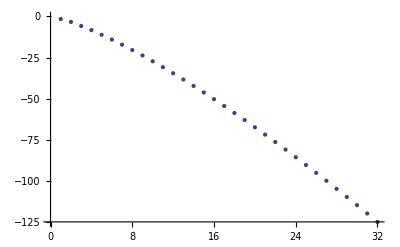

```mathematica
precision=1000;
maxdeviations={};
For[n=0,n<32,n++;
backorbit={};
fx=ls[[n,2]];
For[a=0,j=a<Length[list],a++;
If[list[[a,1]]==n,backorbit=Append[backorbit,list[[a,3]]]]];
prd=plotRelDev7[backorbit,fx,precision];
mprd=Log[Max[prd]];
maxdeviations=Append[maxdeviations,mprd]];
Print["maximum deviations"];
ListPlot[maxdeviations]
```

```mathematica
leaf6point3right
```

maximum deviations

-Graphics-

```mathematica
precision=1000;
meandeviations={};
For[n=0,n<32,n++;
backorbit={};
fx=ls[[n,2]];
For[a=0,j=a<Length[list],a++;
If[list[[a,1]]==n,backorbit=Append[backorbit,list[[a,3]]]]];
prd=plotRelDev7[backorbit,fx,precision];
mprd=Log[Mean[prd]];
meandeviations=Append[meandeviations,mprd]];
Print["mean deviations"];
ListPlot[maxdeviations]
```

mean deviations

-Graphics-

## leaf6point3left

mean deviations